## Reproducing the purification sequence with gates derived from the hamiltonian

```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookDirectory[]
```

/Users/humphreys/Repositories/personal_calcs/Work/Modelling/Purification/Simulations/

This notebook explores the purification sequence by simulating the hamiltonian (in secular approximation).
We aim to synthesize the following gate sequence. With the assumption that we generate a perfect state on the electron spins (i.e. V=1)
-Graphics-

```mathematica
Quiet[Needs["QDENSITY`Qdensity`"]];
Quiet[Needs["QDENSITY`QCWave`"]];
?QDENSITY`Qdensity`*
```

General useful definitions such as gates etc.

```mathematica
KP[r__]:=KroneckerProduct[r]
StyleNumber[number_] :=Style[number,Bold,Darker[Green]]
Stokesfromρ[ρ_]:=(t =Table[Re[Tr[Subscript[σ, i].ρ]],{i,1,3}]//N; t)
StokesfromρStyled[ρ_]:=(t =Table[If[Abs[Re[Tr[Subscript[σ, i].ρ]]]>0.4,StyleNumber[Re[Tr[Subscript[σ, i].ρ]]],Re[Tr[Subscript[σ, i].ρ]]],{i,1,3}]//N; t)
ρfromψ[ψ_] :=ψ.ψ†;
Stokesfromψ[ψ_]:=Stokesfromρ[ρfromψ[ψ]];
Fidfromρ[ρ_,σ_]:=Re[Tr[MatrixPower[MatrixPower[ρ,0.5].σ.MatrixPower[ρ,0.5],0.5]]^2];
MixedState=𝕀/2;(*Mixed state*)
```

```mathematica
(*Single qubit gates*)
{rxp,rXp,ryp,rYp,rzp,rZp}=Table[AF[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[AF[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
rThetaX[θ_]=MatrixExp[-ⅈ*Subscript[σ, 1]*θ/2];
rThetaY[θ_]=MatrixExp[-ⅈ*Subscript[σ, 2]*θ/2];
rThetaZ[θ_]=MatrixExp[-ⅈ*Subscript[σ, 3]*θ/2];
```

Our nuclear spin parameters for both setups:

```mathematica
(*LT3*)
ωL3 = 2*π*447841.28;
Aperp3 =2*π*(87.5)*10^3;
Apar3 = -2*π*(30.0)*10^3 ;

N3 = 12; (*original gate parameters*)
(*N3 = N3-2;(*adjusted for simulation in accuracies*)*)
τ3 = 10.886*10^-6; (*original gate parameters*)
(*τ3 = τ3 -29.1*10^-9;*)

(*LT4*)
ωL4 = 2*π*443180.29;
Aperp4 =2*π*(35.0)*10^3;
Apar4 =-2*π*(33.0)*10^3 ; (*because we use the -1 transition here*)
N4 = 34; (*original gate parameters*)
(*N4 = N4-2; (*adjust fdor simulation*)*)
τ4 = 6.406*10^-6(*original gate parameters*); 
(*τ4 =τ4+14*10^-9(*adjust for simulation*);*)

(*carbon parameters as a list*)
LT3Cinit = {ωL3,Apar3,Aperp3};
LT3Gate = {τ3,N3}; (*Gate parameters have to be slightly adjusted*)
LT4Cinit= {ωL4,Apar4,Aperp4};
LT4Gate = {τ4,N4};(*Gate parameters have to be slightly adjusted*)
```

The system Hamiltonian with NV and Carbon reads

```mathematica
Hsys[ω_,Apar_,Aperp_] = ω*Subscript[𝒫, 0]⊗Subscript[σ, 3]+Subscript[𝒫, 1]⊗((Apar+ω)Subscript[σ, 3]+Aperp*Subscript[σ, 1]);
H0[ω_,Apar_,Aperp_]= ω*Subscript[σ, 3];
H1[ω_,Apar_,Aperp_]=(Apar+ω)Subscript[σ, 3]+Aperp*Subscript[σ, 1];
```

What we want to do is concatenate the evolution operator for a certain π-pulse timing on the NV

```mathematica
U0[τ_,ω_,Apar_,Aperp_]=MatrixExp[-ⅈ*H0[ω,Apar,Aperp]*τ/2]//FullSimplify;
U1[τ_,ω_,Apar_,Aperp_]=MatrixExp[-ⅈ*H1[ω,Apar,Aperp]*τ/2]//FullSimplify;
```

Combine into a nuclear gate:

```mathematica
C13Gate[{τ_,N_},{ω_,Apar_,Aperp_},Eigenphase_]:=(
V0 = U0[τ,ω,Apar,Aperp].U1[τ,ω,Apar,Aperp].U1[τ,ω,Apar,Aperp].U0[τ,ω,Apar,Aperp];
V1 = U1[τ,ω,Apar,Aperp].U0[τ,ω,Apar,Aperp].U0[τ,ω,Apar,Aperp].U1[τ,ω,Apar,Aperp];
V0N = Chop[MatrixPower[V0,N/2],10^-6]//FullSimplify; (*Round to 10^-4*)
V1N = Chop[MatrixPower[V1,N/2],10^-6]//FullSimplify; (*Round to 10^-4*)
(KP[Subscript[𝒫, 0],V0N]+KP[Subscript[𝒫, 1],V1N]).KP[Subscript[σ, 0],rThetaZ[Eigenphase]]
)
```

Generate a fingerprint to check the gate parameters

```mathematica
FP[N_,τ_,{ω_,Apar_,Aperp_}]:=(
initialEstate = ρfromψ[KetX[0]];
Initstate=KP[initialEstate,MixedState]; (*Nuclear spin is in a mixed state*)
sequence = C13Gate[{τ,N},{ω,Apar,Aperp},0];
finalstate = sequence.Initstate.sequence†;
finalEstate = PTr[{2},finalstate];
Fidfromρ[finalEstate,initialEstate]
)
```

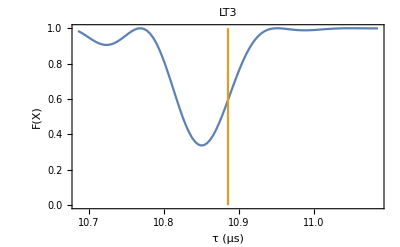
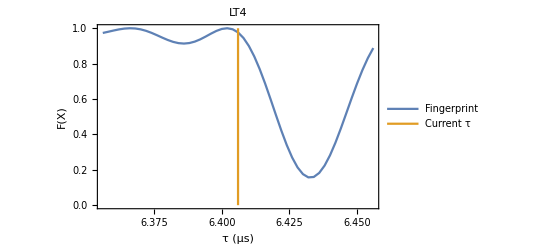
-Graphics- | -Graphics-

```mathematica
FPresults3 = Table[{t,FP[N3,t*10^-6,LT3Cinit]},{t,LT3Gate[[1]]*10^6-0.2,LT3Gate[[1]]*10^6+0.2,0.004}];
FPresults4 = Table[{t,FP[N4,t*10^-6,LT4Cinit]},{t,LT4Gate[[1]]*10^6-0.05,LT4Gate[[1]]*10^6+0.05,0.002}];
plt1=ListPlot[{FPresults3,{{τ3*10^6,0.0},{τ3*10^6,1.0}}},Joined->{True,True},PlotRange->All,Frame->True,FrameLabel->{"τ (μs)","F(X)"},PlotLabel->"LT3"];
plt2 = ListPlot[{FPresults4,{{τ4*10^6,0.0},{τ4*10^6,1.0}}},Joined->{True},PlotRange->All,Frame->True,FrameLabel->{"τ (μs)","F(X)"},PlotLabel->"LT4",PlotLegends->{"Fingerprint","Current τ"}];
Grid[{{plt1,plt2}}]
```

```mathematica
LT3C = {ωL3,Apar3-1.8*^3,Aperp3-51.4*^3};
LT4C={ωL4,Apar4+11.814*^3,Aperp4};

FP[N3,τ3,LT3C]
FP[N4,τ4,LT4C]
```

0.499981

0.500003

```mathematica
(*Create the nuclear spin gate matrices in memory (the system's evolution won't change, so this is precompiled.)*)
GateLT3[Eigenphase_] := C13Gate[LT3Gate,LT3C,Eigenphase];
GateLT4[Eigenphase_] := C13Gate[LT4Gate,LT4C,Eigenphase];
```

## Nuclear spin initialization

Create sequences

```mathematica
NuclearMBISequence[Gate_] := KP[rxp,Subscript[σ, 0]].Gate.KP[ryp,Subscript[σ, 0]];
NuclearSwapSequence[Gate_]:=Gate.KP[rxp,rThetaZ[-π/2.]].Gate.KP[ryp,Subscript[σ, 0]];
```

These functions only initialize the nuclear spin and check the fidelity on the nucleus directly (no tomography applied)

```mathematica
InitializeC13X[Gate_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,MixedState];
sequence = KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearMBISequence[Gate]; (*Last part here constitutes a measurement.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
Fidfromρ[ρfromψ[KetX[0]],PTr[{1},outputstate]]
)
```

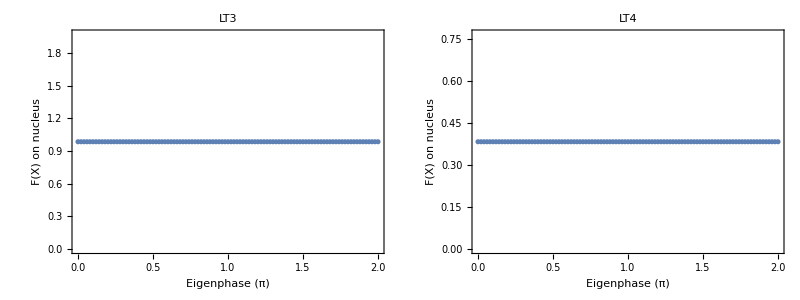

```mathematica
PhaseSweep3= Table[{ϕ,InitializeC13X[GateLT3[π*ϕ]]},{ϕ,0,2,0.02}];
PhaseSweep4= Table[{ϕ,InitializeC13X[GateLT4[π*ϕ]]},{ϕ,0,2,0.02}];
plt1=ListPlot[{PhaseSweep3},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(X) on nucleus"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseSweep4},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(X) on nucleus"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

```mathematica
InitializeC13Z[Gate_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,MixedState];
sequence = NuclearSwapSequence[Gate];
outputstate  = sequence.Initstate.sequence†;
(*outputstate = outputstate/Tr[outputstate];*)
Fidfromρ[ρfromψ[Ket[0]],PTr[{1},outputstate]]
)
```

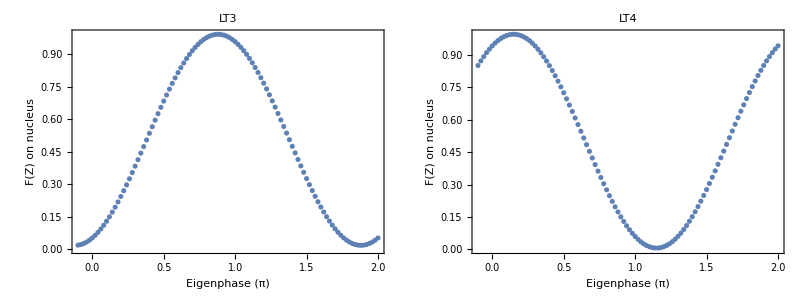

```mathematica
(*Check the state of the nucleus before initialzation directly*)
(*Note that this does not necessarily represent the tomography outcome!!!*)
PhaseSweep3= Table[{ϕ,InitializeC13Z[GateLT3[π*ϕ]]},{ϕ,-0.1,2,0.02}];
PhaseSweep4= Table[{ϕ,InitializeC13Z[GateLT4[π*ϕ]]},{ϕ,-0.1,2,0.02}];
plt1=ListPlot[{PhaseSweep3},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(Z) on nucleus"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseSweep4},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(Z) on nucleus"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

## Nuclear spin init + tomography

Create sequences

```mathematica
TomoXSequence[Gate_] := KP[rxp,Subscript[σ, 0]].Gate.KP[ryp,rThetaZ[0]];
TomoYSequence[Gate_] := KP[rxp,Subscript[σ, 0]].Gate.KP[ryp,rThetaZ[-π/2]];
TomoZSequence[Gate_] := KP[rxp,Subscript[σ, 0]].Gate.KP[ryp,rThetaZ[-π/2.]].Gate;
TomoZSequenceInv[Gate_] := KP[rxp,Subscript[σ, 0]].Gate.KP[ryp,rThetaZ[+π/2.]].Gate;
```

Simulation of the MBI into X experiment

```mathematica
InitTomoX[Gate_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,MixedState];
sequence =TomoXSequence[Gate]. KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearMBISequence[Gate]; (*Part with the projector Subscript[𝒫, 0] constitutes a measurement of the electron.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
Fidfromρ[ρfromψ[Ket[0]],PTr[{2},outputstate]]
)
```

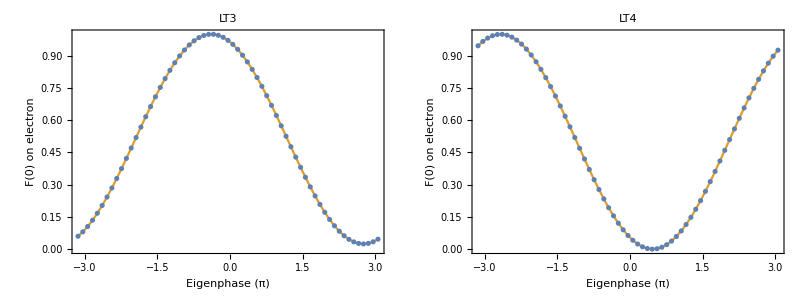

```mathematica
PhaseSweep3= Table[{ϕ,InitTomoX[GateLT3[ϕ]]},{ϕ,-π,π,0.1}];
PhaseSweep4= Table[{ϕ,InitTomoX[GateLT4[ϕ]]},{ϕ,-π,π,0.1}];
nlmLT3=NonlinearModelFit[PhaseSweep3,Amp(1+Cos[ x+a])/2+offset,{{a,π},{Amp,1},{offset,0}},x];
fitPts1=Table[{x,Normal[nlmLT3[x]]},{x,-π,π,0.1}];
nlmLT4=NonlinearModelFit[PhaseSweep4,Amp(1+Cos[ x+a])/2+offset,{{a,π},{Amp,1},{offset,0}},x];
fitPts2=Table[{x,Normal[nlmLT4[x]]},{x,-π,π,0.1}];
plt1=ListPlot[{PhaseSweep3,fitPts1},Joined->{False,True},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(0) on electron"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseSweep4,fitPts2},Joined->{False,True},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

```mathematica
eigenPhaseLT3=If[Amp>0,a,Mod[a+π,2π]]/.nlmLT3["BestFitParameters"]
eigenPhaseLT4=If[Amp>0,a,Mod[a+π,2π]]/.nlmLT4["BestFitParameters"]
```

0.38545

2.67357

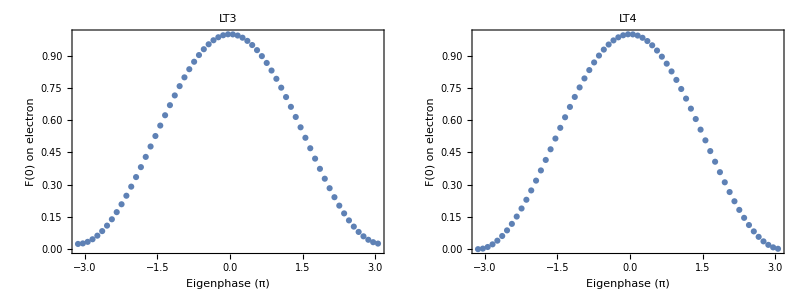

```mathematica
PhaseSweep3= Table[{ϕ,InitTomoX[GateLT3[ϕ-eigenPhaseLT3]]},{ϕ,-π,π,0.1}];
PhaseSweep4= Table[{ϕ,InitTomoX[GateLT4[ϕ-eigenPhaseLT4]]},{ϕ,-π,π,0.1}];
plt1=ListPlot[{PhaseSweep3},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(0) on electron"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseSweep4},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

Initialize X and read-out Y

```mathematica
InitXTomoY[Gate_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,MixedState];
sequence =TomoYSequence[Gate]. KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearMBISequence[Gate]; (*Part with the projector Subscript[𝒫, 0] constitutes a measurement of the electron.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
Fidfromρ[ρfromψ[Ket[0]],PTr[{2},outputstate]]
)
```

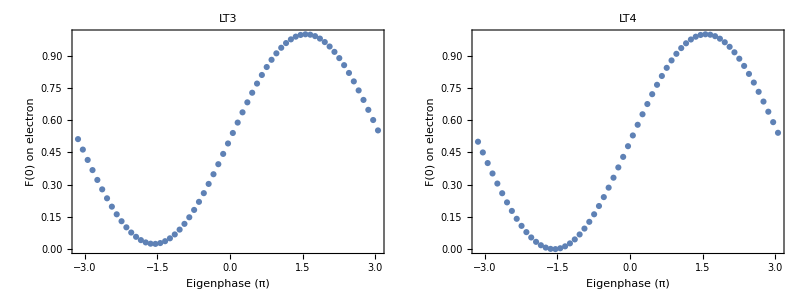

```mathematica
PhaseSweep3= Table[{ϕ,InitXTomoY[GateLT3[ϕ-eigenPhaseLT3]]},{ϕ,-π,π,0.1}];
PhaseSweep4= Table[{ϕ,InitXTomoY[GateLT4[ϕ-eigenPhaseLT4]]},{ϕ,-π,π,0.1}];
plt1=ListPlot[{PhaseSweep3},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(0) on electron"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseSweep4},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Eigenphase (π)","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

Simulating the SWAP onto Z experiment

```mathematica
InitTomoZ[Gate_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];
sequence =TomoZSequence[Gate].NuclearSwapSequence[Gate]; (*Part with the projector Subscript[𝒫, 0] constitutes a measurement of the electron.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
Fidfromρ[ρfromψ[Ket[0]],PTr[{2},outputstate]]
)
```

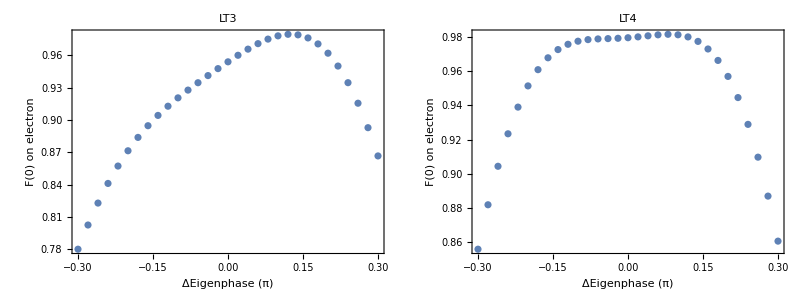

```mathematica
PhaseSweep3= Table[{ϕ,InitTomoZ[GateLT3[π*ϕ-eigenPhaseLT3]]},{ϕ,-0.3,0.3,0.02}];
PhaseSweep4= Table[{ϕ,InitTomoZ[GateLT4[π*ϕ-eigenPhaseLT4]]},{ϕ,-0.3,0.3,0.02}];
plt1=ListPlot[{PhaseSweep3},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"ΔEigenphase (π)","F(0) on electron"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseSweep4},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"ΔEigenphase (π)","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

```mathematica
(*Interesting structure... but i guess that comes from me botching the gate parameters.*)
```

## Init + swap + tomo

How do you swap? Well here is the sequence.
We want to implement this snippet of the sequence:
-Graphics-

```mathematica
SwapSequenceLocal[Gate_,Electrongate_]:=KP[rym,Subscript[σ, 0]].Gate.KP[rxp,Subscript[σ, 0]].Gate.KP[Electrongate,rThetaZ[-π/2]]

SwapSequenceNonLocal[Gate_]:=KP[rym,Subscript[σ, 0]].Gate.KP[rxp,Subscript[σ, 0]].Gate.KP[rXp,rThetaZ[-π/2]] (*non local needs less arguments*)
```

```mathematica
InitSwapTomoZ[Gate_,Electrongate_,TomoSequence_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];
sequence =TomoSequence.KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceLocal[Gate,Electrongate].KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[Gate] //FullSimplify; (*Part with the projector Subscript[𝒫, 0] constitutes a measurement of the electron.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
retval = Round[2*(Fidfromρ[ρfromψ[Ket[0]],PTr[{2},outputstate]]-0.5),0.01];
If[Abs[retval]>0.4,Style[retval,Bold,Darker[Green]],retval]
)
TomosLT3 = {TomoXSequence[GateLT3[-eigenPhaseLT3]],TomoYSequence[GateLT3[-eigenPhaseLT3]],TomoZSequence[GateLT3[-eigenPhaseLT3]]};
TomosLT4 = {TomoXSequence[GateLT4[-eigenPhaseLT4]],TomoYSequence[GateLT4[-eigenPhaseLT4]],TomoZSequence[GateLT4[-eigenPhaseLT4]]};
electronGates = { rXp.Subscript[σ, 0], rXp.rXp, rXp.ryp, rXp.rym, rXp.rxp, rXp.rxm};
swapResultsLT3=Table[{Flatten[pulse.Ket[0]]*Exp[-ⅈ Arg[Flatten[pulse.Ket[0]][[1]]]],InitSwapTomoZ[GateLT3[-eigenPhaseLT3],pulse,TomosLT3[[1]]],InitSwapTomoZ[GateLT3[-eigenPhaseLT3],pulse,TomosLT3[[2]]],InitSwapTomoZ[GateLT3[-eigenPhaseLT3],pulse,TomosLT3[[3]]]},{pulse,electronGates}];
swapResultsLT4=Table[{Flatten[pulse.Ket[0]]*Exp[-ⅈ Arg[Flatten[pulse.Ket[0]][[1]]]],InitSwapTomoZ[GateLT4[-eigenPhaseLT4],pulse,TomosLT4[[1]]],InitSwapTomoZ[GateLT4[-eigenPhaseLT4],pulse,TomosLT4[[2]]],InitSwapTomoZ[GateLT4[-eigenPhaseLT4],pulse,TomosLT4[[3]]]},{pulse,electronGates}];
Print["LT3"]
Grid[Catenate[{{{"electron input", "<X>","<Y>","<Z>"}},swapResultsLT3}],Frame->All]
Print["LT4"]
Grid[Catenate[{{{"electron input", "<X>","<Y>","<Z>"}},swapResultsLT4}],Frame->All]
```

LT3

electron input | <X> | <Y> | <Z>
{0,-ⅈ} | -1. | -0.02 | -0.02
{1,0} | 1. | 0.02 | 0.02
{1/(√2),1/(√2)} | 0.36 | 0.39 | 0.84
{1/(√2),-1/(√2)} | 0.36 | -0.37 | -0.82
{1/(√2),ⅈ/(√2)} | 0.36 | 0.86 | -0.42
{1/(√2),-ⅈ/(√2)} | 0.36 | -0.84 | 0.44

LT4

electron input | <X> | <Y> | <Z>
{0,-ⅈ} | -1. | 0. | 0.
{1,0} | 1. | 0. | 0.
{1/(√2),1/(√2)} | -0.16 | -0.28 | 0.9
{1/(√2),-1/(√2)} | -0.16 | 0.28 | -0.9
{1/(√2),ⅈ/(√2)} | -0.16 | 0.95 | 0.4
{1/(√2),-ⅈ/(√2)} | -0.16 | -0.95 | -0.4

```mathematica
(*What if we get the carbon state directly:does the swap do the same for both setups??*)
InitSwapZ[Gate_,Electrongate_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];
sequence =KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceLocal[Gate,Electrongate].KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[Gate] //FullSimplify; (*Part with the projector Subscript[𝒫, 0] constitutes a measurement of the electron.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
retval =StokesfromρStyled[Round[PTr[{1},outputstate],0.01]]
)
```

```mathematica
swapResultsLT3=Table[{Flatten[pulse.Ket[0]]*Exp[-ⅈ Arg[Flatten[pulse.Ket[0]][[1]]]],InitSwapZ[GateLT3[-eigenPhaseLT3],pulse]},{pulse,electronGates}];
swapResultsLT4=Table[{Flatten[pulse.Ket[0]]*Exp[-ⅈ Arg[Flatten[pulse.Ket[0]][[1]]]],InitSwapZ[GateLT4[-eigenPhaseLT4],pulse]},{pulse,electronGates}];
Grid[Catenate[{{{"electron input ψ", "         <X> , <Y> , <Z> carbon"}},swapResultsLT3}],Frame->All]
Grid[Catenate[{{{"electron input ψ","         <X> , <Y> , <Z> carbon"}},swapResultsLT4}],Frame->All]
```

electron input ψ |          <X> , <Y> , <Z> carbon
{0,-ⅈ} | {-0.96,-0.18,0.16}
{1,0} | {0.96,0.18,-0.16}
{1/(√2),1/(√2)} | {0.16,0.28,-0.94}
{1/(√2),-1/(√2)} | {0.54,-0.14,0.84}
{1/(√2),ⅈ/(√2)} | {0.22,0.96,0.18}
{1/(√2),-ⅈ/(√2)} | {0.48,-0.82,-0.3}

electron input ψ |          <X> , <Y> , <Z> carbon
{0,-ⅈ} | {0.24,0.98,-0.02}
{1,0} | {-0.24,-0.98,0.02}
{1/(√2),1/(√2)} | {-0.22,0.2,-0.96}
{1/(√2),-1/(√2)} | {0.3,0.1,0.94}
{1/(√2),ⅈ/(√2)} | {0.96,-0.06,-0.26}
{1/(√2),-ⅈ/(√2)} | {-0.88,0.38,0.26}

## Find the phase of the last cnot gate for both setups (calibrate phase_offset_z)

```mathematica
(*calculate some arbitraty phase after one repetition of the LDE element*)
AcquiredPhaseGate[τLarmor_,τrep_,{ω_,Apar_,Aperp_}]=(
τ0 = (7-τLarmor+τrep)*10^-6;
evolve0 = U1[τLarmor-τrep,ω,Apar,Aperp].U0[τ0,ω,Apar,Aperp];
evolve1 = U0[τLarmor-τrep,ω,Apar,Aperp].U1[τ0,ω,Apar,Aperp];
KP[Subscript[𝒫, 0],evolve0]+KP[Subscript[𝒫, 1],evolve1]
);
OneLDELT3 = AcquiredPhaseGate[2π*10^6/ωL3,0.22,LT3C]; (*Repumping is assumed to be instantaneous*)
OneLDELT4 = AcquiredPhaseGate[2π*10^6/ωL4,0.25,LT4C]; (*Repumping is assumed to be instantaneous*)
```

```mathematica
(*This is how we compensate the phase on the nuclei by decoupling*)
PhaseCompGate[τPhase_,{ω_,Apar_,Aperp_}]=(
evolve0 =U0[τPhase,ω,Apar,Aperp]. U1[τPhase,ω,Apar,Aperp].U1[τPhase,ω,Apar,Aperp].U0[τPhase,ω,Apar,Aperp];
evolve1 =U1[τPhase,ω,Apar,Aperp]. U0[τPhase,ω,Apar,Aperp].U0[τPhase,ω,Apar,Aperp].U1[τPhase,ω,Apar,Aperp];
KP[Subscript[𝒫, 0],evolve0]+KP[Subscript[𝒫, 1],evolve1]
);
OnePhaseLT3 = PhaseCompGate[2.261*10^-6,LT3C];
OnePhaseLT4 = PhaseCompGate[2.31*10^-6,LT4C];
```

```mathematica
(*Phase per PhaseCompensationGate*)
CalibratePhaseComp[Gate_,LDE_,PhaseCompGate_]:=(
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];
sequence =TomoXSequence[Gate].PhaseCompGate.(KP[Subscript[𝒫, 0],Subscript[σ, 0]]+KP[Subscript[σ, 1].Subscript[𝒫, 1],Subscript[σ, 0]]).LDE.KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceLocal[Gate,rXp].KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[Gate] //FullSimplify; (*Part with the projector Subscript[𝒫, 0] constitutes a measurement of the electron.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
retval = Round[2*(Fidfromρ[ρfromψ[Ket[0]],PTr[{2},outputstate]]-0.5),0.01];
retval
)
```

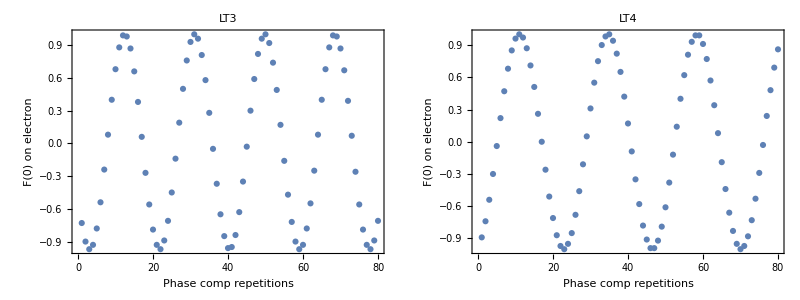

```mathematica
PhaseCompSweep3= Table[{iterations,CalibratePhaseComp[GateLT3[-eigenPhaseLT3],OneLDELT3,MatrixPower[OnePhaseLT3,iterations]]},{iterations,1,80,1}];
PhaseCompSweep4= Table[{iterations,CalibratePhaseComp[GateLT4[-eigenPhaseLT4],OneLDELT4,MatrixPower[OnePhaseLT4,iterations]]},{iterations,1,80,1}];
plt1=ListPlot[{PhaseCompSweep3},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Phase comp repetitions","F(0) on electron"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseCompSweep4},Joined->{False},PlotRange->All,Frame->True,FrameLabel->{"Phase comp repetitions","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

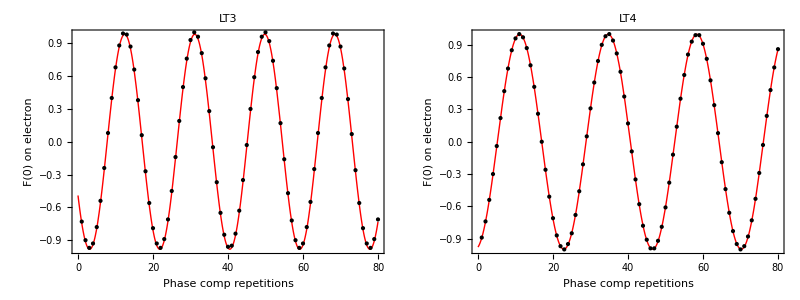

```mathematica
(*One can then fit the result and get a phase per compensation repetition for both setups*)
nlmLT3=NonlinearModelFit[PhaseCompSweep3,Amp*Sin[f*x+a],{{f,2π*16.28/360},{a,π},{Amp,1}},x];plt1=Plot[Normal[nlmLT3[x]],{x,0,80},Epilog:>Point[PhaseCompSweep3],PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Phase comp repetitions","F(0) on electron"},PlotLabel->"LT3"];
nlmLT4=NonlinearModelFit[PhaseCompSweep4,Amp*Sin[f*x+a],{{f,2π*20/360},{a,π},{Amp,1}},x];plt2=Plot[Normal[nlmLT4[x]],{x,0,80},Epilog:>Point[PhaseCompSweep4],PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Phase comp repetitions","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

```mathematica
(*Extract a phase per compensation repetition from the fit*)
phasecompLT3 = 360*f/(2π)/.nlmLT3["BestFitParameters"]
phasecompLT4 = 360*f/(2π)/.nlmLT4["BestFitParameters"]
```

19.2732

15.2226

```mathematica
(*This function decides how many phase compensation repetitions to make and what gate is being applied to the electron and Nuclearspin*)
CalculatePhaserepetitions[ϕInput_,ϕComp_,ϕout_]:=(
ϕdiff = Mod[ϕout-ϕInput,360];
(*this is what the adwin does*)
If[ϕdiff<0,ϕdiff = 360+ϕdiff]; (*make sure it is positive*) 
For[i=1,i<500,i++,(
ϕtot=Mod[ϕComp*i,360];
If[(Abs[Mod[ϕtot-ϕdiff,360]]<2)||(Abs[360-(ϕtot-ϕdiff)]<2),(iout=i;Break[]),iout=i];)(*set two degrees accuracy*)
];
iout
)
CreatePhaseGate[ϕInput_,ϕComp_,ϕout_,OnePhaseGate_]:=(
iout=CalculatePhaserepetitions[ϕInput,ϕComp,ϕout];
phaseGate = MatrixPower[OnePhaseGate,iout];
(*And the electron gate*)
If[Mod[iout,2] ==0,eGate=MatrixPower[(rYp.rXp),iout];,eGate =rXm.rXp.MatrixPower[(rYp.rXp),iout-1];];
(*Return the compiled gate operation*)
(*Print[iout];*)
KP[eGate,Subscript[σ, 0]].phaseGate
)
```

```mathematica
(*Now off to the calibration routine:*)
(*This function is compiled without the LDE element, any carbon evolution during the LDe element is therefore ignored*)
```

```mathematica
CalibratePhaseOffsetZ[GateFunction_,Eigenphase_,ϕoffset_,PhaseGate_,phasecomp_]:=(
(*compile the sequence*)
CompiledGate=GateFunction[Eigenphase];
initEstate=Ket[0].Ket[0]†;
Initstate = KP[initEstate,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];(*The implementation of the LDE element is not entirely correct!*)
phasegate = CreatePhaseGate[0,phasecomp,ϕoffset,PhaseGate];
repetitions = CalculatePhaserepetitions[0,phasecomp,ϕoffset];
sequence =TomoZSequence[CompiledGate].KP[Subscript[𝒫, 0],Subscript[σ, 0]].GateFunction[0].KP[ryp,Subscript[σ, 0]].phasegate.(KP[rXp.rym,Subscript[σ, 0]]).KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceLocal[CompiledGate,rXp.rxp].KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[CompiledGate] //FullSimplify; (*Part with the projector Subscript[𝒫, 0] constitutes a measurement of the electron.*)
outputstate  = sequence.Initstate.sequence†;
outputstate = outputstate/Tr[outputstate];
retval = Round[2*(Fidfromρ[ρfromψ[Ket[0]],PTr[{2},outputstate]]-0.5),0.01];
{retval,repetitions}
)
SimulatePhaseOffsetZLT3[Offset_] := CalibratePhaseOffsetZ[GateLT3,-eigenPhaseLT3,Offset,OnePhaseLT3,phasecompLT3]
SimulatePhaseOffsetZLT4[Offset_]:=  CalibratePhaseOffsetZ[GateLT4,-eigenPhaseLT4,Offset,OnePhaseLT4,phasecompLT4]
```

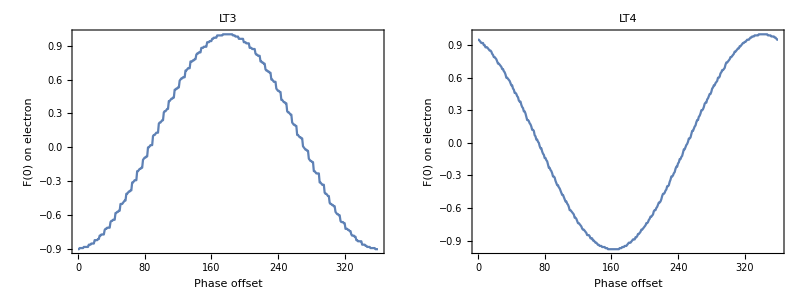

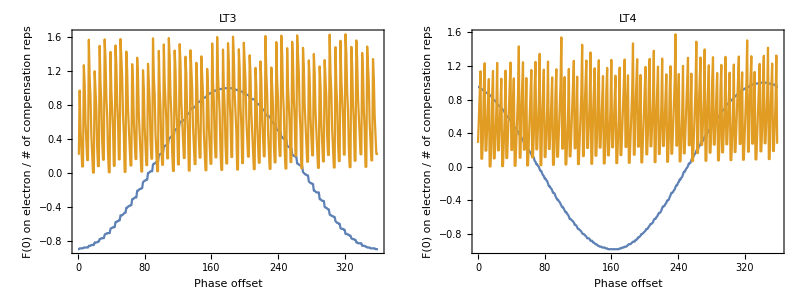

```mathematica
PhaseoffsetSweep3= Table[{phaseoffset,SimulatePhaseOffsetZLT3[phaseoffset][[1]]},{phaseoffset,0,360,1}];
PhaseoffsetSweep4= Table[{phaseoffset,SimulatePhaseOffsetZLT4[phaseoffset][[1]]},{phaseoffset,0,360,1}];
NoOfReps3= Table[{phaseoffset,SimulatePhaseOffsetZLT3[phaseoffset][[2]]/250},{phaseoffset,0,360,1}];
NoOfReps4= Table[{phaseoffset,SimulatePhaseOffsetZLT4[phaseoffset][[2]]/250},{phaseoffset,0,360,1}];
plt1=ListPlot[{PhaseoffsetSweep3},Joined->{True},PlotRange->All,Frame->True,FrameLabel->{"Phase offset","F(0) on electron"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseoffsetSweep4},Joined->{True},PlotRange->All,Frame->True,FrameLabel->{"Phase offset","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
plt1=ListPlot[{PhaseoffsetSweep3,NoOfReps3},Joined->{True},PlotRange->All,Frame->True,FrameLabel->{"Phase offset","F(0) on electron / # of compensation reps"},PlotLabel->"LT3"];
plt2=ListPlot[{PhaseoffsetSweep4,NoOfReps4},Joined->{True},PlotRange->All,Frame->True,FrameLabel->{"Phase offset","F(0) on electron / # of compensation reps"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

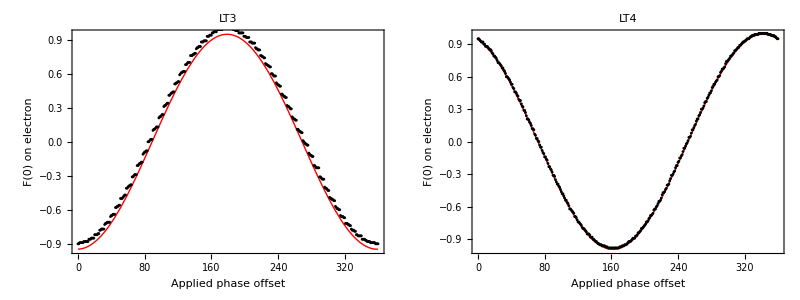

```mathematica
(*With this we can again use our fitting routine to determine the phase offset*)
(*One can then fit the result and get a phase per compensation repetition for both setups*)
nlmLT3=NonlinearModelFit[PhaseoffsetSweep3,Amp*Cos[2π*x/360-a],{{a,π},{Amp,1}},x];plt1=Plot[Normal[nlmLT3[x]],{x,0,360},Epilog:>{PointSize[0.005],Point[PhaseoffsetSweep3]},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Applied phase offset","F(0) on electron"},PlotLabel->"LT3"];
nlmLT4=NonlinearModelFit[PhaseoffsetSweep4,Amp*Cos[2π*x/360-a],{{a,π},{Amp,1}},x];plt2=Plot[Normal[nlmLT4[x]],{x,0,360},Epilog:>{PointSize[0.005],Point[PhaseoffsetSweep4]},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Applied phase offset","F(0) on electron"},PlotLabel->"LT4"];
Grid[{{plt1,plt2}}]
```

```mathematica
(*Extract the phase offset from the fit. One needs to take the sign of the fit function into account*)
phaseoffsetLT3 = (180*a/π+180*(1-Sign[Amp])/2)/.nlmLT3["BestFitParameters"]
phaseoffsetLT4 = (180*a/π+180*(1-Sign[Amp])/2)/.nlmLT4["BestFitParameters"]
```

178.925

341.895

```mathematica
(*Let's try if this works:*)
```

```mathematica
SimulatePhaseOffsetZLT3[phaseoffsetLT3]
SimulatePhaseOffsetZLT4[phaseoffsetLT4]
```

(1.
28)

(1.
259)

```mathematica
(*Full purification sequence on a single node with classical correlations as input (introduced via the swap)*)
ClassCorrAndFullPurification[Gatefunc_,Eigenphase_,ROProjection_,TomoCircuit_,inputpulse_]:=(
(*For simplicity I calculate everything for one setup: LT3.*)
(*Get prelim definitions in*)
CompGLT3 = Gatefunc[Eigenphase];

Initstate = KP[Ket[0].Ket[0]†,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];(*pure (electron) and completely mixed (nucleus)*)
phasegateLT3 = CreatePhaseGate[0,phasecompLT3,phaseoffsetLT3,OnePhaseLT3];

(*Put individual parts of the sequence together*)
C13InitLT3 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[CompGLT3];
SwapSeqLT3 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceNonLocal[CompGLT3].KP[inputpulse,Subscript[σ, 0]];
PhaseCompLT3=phasegateLT3.KP[rXp.rxp,Subscript[σ, 0]];
PurifyGateLT3 = KP[ROProjection.rxp,Subscript[σ, 0]].Gatefunc[0].KP[ryp,Subscript[σ, 0]];


(*Tomos are supplied as arguments/matrices. Have to include a 180 degree phase shift due to the reset.*)
Tomo = TomoCircuit.KP[Subscript[σ, 0],rZp];

(*Run the sequence*)
(*First initialize the C13s into Z*)
ρ = C13InitLT3.Initstate.C13InitLT3†;
(*swap onto nuclei*)
ρ = SwapSeqLT3.ρ.SwapSeqLT3†;
(*pretend to generate another entangled pair and perform phaes compensation+purification gate*)
ρ = (PurifyGateLT3.PhaseCompLT3).ρ.(PurifyGateLT3.PhaseCompLT3)†;
ρ = ρ/Tr[ρ];
(*Apply tomo sequence, trace over the nuclear state and return the electron spin state*)
electronsAfterTomo = Chop[PTr[{2},Tomo.ρ.Tomo†]];
(*We always RO the Z projection of the electron --> compute that specific expectation value and return it*)
Tr[electronsAfterTomo.Subscript[σ, 3]]
)
```

```mathematica
ROprojection = Subscript[𝒫, 0];
inputpulse =ryp; (*Subscript[σ, 0],rxp,ryp*)
gate = GateLT3;
ϕ = 1.03π;
Tomos=TomosLT3;
Print["For ms = 0"]
Print[ "Tomo in X:  "<>ToString[ClassCorrAndFullPurification[gate,ϕ,ROprojection,Tomos[[1]],inputpulse]]]
Print[ "Tomo in Y:  "<>ToString[ClassCorrAndFullPurification[gate,ϕ,ROprojection,Tomos[[2]],inputpulse]]]
Print[ "Tomo in Z:  "<>ToString[ClassCorrAndFullPurification[gate,ϕ,ROprojection,Tomos[[3]],inputpulse]]]
ROprojection = Subscript[𝒫, 1];
Print["For ms = ±1"]
Print[ "Tomo in X:  "<>ToString[-ClassCorrAndFullPurification[gate,ϕ,ROprojection,Tomos[[1]],inputpulse]]]
Print[ "Tomo in Y:  "<>ToString[-ClassCorrAndFullPurification[gate,ϕ,ROprojection,Tomos[[2]],inputpulse]]]
Print[ "Tomo in Z:  "<>ToString[ClassCorrAndFullPurification[gate,ϕ,ROprojection,Tomos[[3]],inputpulse]]]
```

For ms = 0

Tomo in X:  -0.392404

Tomo in Y:  0.719142

Tomo in Z:  -0.613791

For ms = ±1

Tomo in X:  -0.0567194

Tomo in Y:  -0.705691

Tomo in Z:  0.750218

## Init + swap + purification (the first non-local msmt) & look at internal nuclear state

The main problem here is that all gates naturally act on adjacent qubits and expect states of the form ρ_NV⊗ρ_C (or other non separable states of this ordering).
This gives the natural order for the qubits: {NV_1,C_1,NV_2,C_2}. States are however generated on the NVs directly. 
Therefore,Need to find a way to change order in density matrices....
Such that (the operator ⊗ is symbolical here):
ρ_(NV_1 NV_2)⊗ρ_(C_1 C_2) = ρ_(NV_1 C_1 NV_2 C_2)

```mathematica
(*This function brute forces the problem by looping over all expectation values
This probably not the most efficient method but good enough for 16x16 matrices*)
Raffleρ4Q[ρ_]:=(
ρNew = ConstantArray[0,{16,16}] ;(*Init matrix*)
Do[ρNew+=0.5^4*Tr[KP[Subscript[σ, i],Subscript[σ, j],Subscript[σ, k],Subscript[σ, l]].ρ]*KP[Subscript[σ, i],Subscript[σ, k],Subscript[σ, j],Subscript[σ, l]],{i,0,3},{j,0,3},{k,0,3},{l,0,3}];
ρNew
)
```

#### Testing the qubit interchanger

```mathematica
ρTest =ρfromψ[KP[KetX[0],KetX[1]]]
```

(1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4
1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4)

```mathematica
ρComb=KP[ρTest,ρTest];
ρRaff=Raffleρ4Q[ρComb];
PTr[{1,2},ρRaff]
PTr[{3,4},ρRaff]
```

(0.25+0. ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ
-0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ
-0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ
0.25+0. ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ)

(0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ)

#### Purification

This function runs the purification protocol and prints the state (ρ) of the two nuclei after a succesful event

```mathematica
PurifyNoTomo[GatefuncLT3_,GatefuncLT4_,EigenphaseLT3_,EigenphaseLT4_]:=(

(*Get prelim definitions in*)
rawState = 0.5*ρfromψ[KP[Ket[0],Ket[0]]]+0.5*ρfromψ[1/(√2)*(KP[Ket[0],Ket[1]]+KP[Ket[1],Ket[0]])];
CompGLT3 = GatefuncLT3[EigenphaseLT3];
CompGLT4 = GatefuncLT4[EigenphaseLT4];
Initstate = KP[Ket[0].Ket[0]†,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];(*Valid for both sides*)
phasegateLT3 = CreatePhaseGate[0,phasecompLT3,phaseoffsetLT3,OnePhaseLT3];
phasegateLT4 = CreatePhaseGate[0,phasecompLT4,phaseoffsetLT4,OnePhaseLT4];

(*Put individual parts of the sequence together*)

C13InitLT3 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[CompGLT3];
C13InitLT4 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[CompGLT4];
C13Init = KP[C13InitLT3,C13InitLT4];

SwapSeqLT3 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceNonLocal[CompGLT3];
SwapSeqLT4 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceNonLocal[CompGLT4];
SwapOntoC13 = KP[SwapSeqLT3,SwapSeqLT4];

PhaseCompLT3=phasegateLT3.KP[rXp,Subscript[σ, 0]];
PhaseCompLT4=phasegateLT4.KP[rXp,Subscript[σ, 0]];
PhaseComp = KP[PhaseCompLT3,PhaseCompLT4];

PurifyGateLT3 = KP[Subscript[𝒫, 0].rxp,Subscript[σ, 0]].GatefuncLT3[0].KP[ryp,Subscript[σ, 0]];
PurifyGateLT4 = KP[Subscript[𝒫, 0].rxp,Subscript[σ, 0]].GatefuncLT4[0].KP[ryp,Subscript[σ, 0]];
Purification = KP[PurifyGateLT3,PurifyGateLT4];

(*Run the sequence*)
(*First initialize the C13s into Z*)
C13states = PTr[{1,3},C13Init.KP[Initstate,Initstate].C13Init†];
C13states = Chop[C13states/Tr[C13states]];
(*generate entanglement and swap onto nuclei*)
eStates = rawState;
ρComb = Raffleρ4Q[KP[eStates,C13states]];
C13states = PTr[{1,3},SwapOntoC13.ρComb.SwapOntoC13†];
C13states = Chop[C13states/Tr[C13states]];

(*generate another entangled pair and perform phaes compensation+purification gate*)
ρComb = Raffleρ4Q[KP[eStates,C13states]];
ρComb = (Purification.PhaseComp).ρComb.(Purification.PhaseComp)†;
ρComb = ρComb/Tr[ρComb];

(*Trace over the electron states and return the nuclear spin state*)
c13state = Round[Chop[PTr[{1,3},ρComb]],0.01]
)
```

```mathematica
(*Clearly, this state is entangled*)
PurifyNoTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4]
```

(0.46 | -0.1+0.14 ⅈ | -0.11-0.05 ⅈ | 0.01-0.44 ⅈ
-0.1-0.14 ⅈ | 0.08 | 0.01+0.05 ⅈ | -0.13+0.1 ⅈ
-0.11+0.05 ⅈ | 0.01-0.05 ⅈ | 0.04 | 0.05+0.1 ⅈ
0.01+0.44 ⅈ | -0.13-0.1 ⅈ | 0.05-0.1 ⅈ | 0.42)

## Init + swap + purification including tomo

```mathematica
PurifyTomo[GatefuncLT3_,GatefuncLT4_,EigenphaseLT3_,EigenphaseLT4_,TomoLT3_,TomoLT4_]:=(

(*Get prelim definitions in*)
rawState = 0.5*ρfromψ[KP[Ket[0],Ket[0]]]+0.5*ρfromψ[1/(√2)*(KP[Ket[0],Ket[1]]+KP[Ket[1],Ket[0]])];
CompGLT3 = GatefuncLT3[EigenphaseLT3];
CompGLT4 = GatefuncLT4[EigenphaseLT4];
Initstate = KP[Ket[0].Ket[0]†,0.5(Subscript[𝒫, 0]+Subscript[𝒫, 1])];(*Valid for both sides*)
phasegateLT3 = CreatePhaseGate[0,phasecompLT3,phaseoffsetLT3,OnePhaseLT3];
phasegateLT4 = CreatePhaseGate[0,phasecompLT4,phaseoffsetLT4,OnePhaseLT4];

(*Put individual parts of the sequence together*)

C13InitLT3 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[CompGLT3];
C13InitLT4 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].NuclearSwapSequence[CompGLT4];
C13Init = KP[C13InitLT3,C13InitLT4];

SwapSeqLT3 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceNonLocal[CompGLT3];
SwapSeqLT4 = KP[Subscript[𝒫, 0],Subscript[σ, 0]].SwapSequenceNonLocal[CompGLT4];
SwapOntoC13 = KP[SwapSeqLT3,SwapSeqLT4];

PhaseCompLT3=phasegateLT3.KP[rXp,Subscript[σ, 0]];
PhaseCompLT4=phasegateLT4.KP[rXp,Subscript[σ, 0]];
PhaseComp = KP[PhaseCompLT3,PhaseCompLT4];

PurifyGateLT3 = KP[Subscript[𝒫, 0].rxp,Subscript[σ, 0]].GatefuncLT3[0].KP[ryp,Subscript[σ, 0]];
PurifyGateLT4 = KP[Subscript[𝒫, 0].rxp,Subscript[σ, 0]].GatefuncLT4[0].KP[ryp,Subscript[σ, 0]];
Purification = KP[PurifyGateLT3,PurifyGateLT4];

(*Tomos are supplied as arguments/matrices*)
Tomo = KP[TomoLT3.KP[Subscript[σ, 0],rZp],TomoLT4.KP[Subscript[σ, 0],rZp]];

(*Run the sequence*)
(*First initialize the C13s into Z*)
C13states = PTr[{1,3},C13Init.KP[Initstate,Initstate].C13Init†];
C13states = Chop[C13states/Tr[C13states]];
(*generate entanglement and swap onto nuclei*)
eStates = rawState;
ρComb = Raffleρ4Q[KP[eStates,C13states]];
C13states = PTr[{1,3},SwapOntoC13.ρComb.SwapOntoC13†];
C13states = Chop[C13states/Tr[C13states]];

(*generate another entangled pair and perform phaes compensation+purification gate*)
ρComb = Raffleρ4Q[KP[KP[Subscript[σ, 0],Subscript[σ, 0]].eStates.KP[Subscript[σ, 0],Subscript[σ, 0]]†,C13states]]; (*If you insert a rotation --> generate psi minus.*)
ρComb = (Purification.PhaseComp).ρComb.(Purification.PhaseComp)†;
ρComb = ρComb/Tr[ρComb];
(*Apply tomo sequence, trace over the nuclear states and return the electron spin state*)
electronsAfterTomo = Chop[PTr[{2,4},Tomo.ρComb.Tomo†]];
(*We always RO the ZZ parity of the electrons --> compute that specific expectation value and return it*)
Tr[electronsAfterTomo.KP[Subscript[σ, 3],Subscript[σ, 3]]]
)
```

```mathematica
(*XX*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3[[1]],TomosLT4[[1]]]
(*YY*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3[[2]],TomosLT4[[2]]]
(*ZZ*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3[[3]],TomosLT4[[3]]]
```

-0.951827

0.71105

0.601812

```mathematica
(*The tomography appears to be physical.
For the tested signature (the same detector clicks twice) we measure 
XX= -1
YY = 1
ZZ = -1
See also OneNote 2016-07-23 First combined analysis for the measured results.*)
```

```mathematica
(*what if one inverts the Z tomography??*)
TomosLT3ZInv = {TomoXSequence[GateLT3[-eigenPhaseLT3]],TomoYSequence[GateLT3[0.0π]],TomoZSequenceInv[GateLT3[0.0π]]};
TomosLT4ZInv = {TomoXSequence[GateLT4[-eigenPhaseLT4]],TomoYSequence[GateLT4[+1.03*π]],TomoZSequenceInv[GateLT4[+1.03*π]]};
(*XX*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3ZInv[[1]],TomosLT4ZInv[[1]]]
(*YY*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3ZInv[[2]],TomosLT4ZInv[[2]]]
(*-Z-Z*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3ZInv[[3]],TomosLT4ZInv[[3]]]
```

-0.951827

0.721031

0.768257

```mathematica
(*More tomography games --> what if there is an asymmetric number of Z rotations on both sides?*)
TomoZSequenceZRot[Gate_,power_] := KP[rxp,Subscript[σ, 0]].Gate.KP[ryp,MatrixPower[rZp,2*power].rThetaZ[-π/2.]].Gate;
TomosLT3ZRot = {TomoXSequence[GateLT3[0.0π]],TomoYSequence[GateLT3[0.0π]],TomoZSequenceZRot[GateLT3[0.0π],1]};
TomosLT4ZRot = {TomoXSequence[GateLT4[+1.03*π]],TomoYSequence[GateLT4[+1.03*π]],TomoZSequenceZRot[GateLT4[+1.03*π],2]};
(*XX*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3ZRot[[1]],TomosLT4ZRot[[1]]]
(*YY*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3ZRot[[2]],TomosLT4ZRot[[2]]]
(*ZZ*)
PurifyTomo[GateLT3,GateLT4,-eigenPhaseLT3,-eigenPhaseLT4,TomosLT3ZRot[[3]],TomosLT4ZRot[[3]]]
```

-0.950945

0.721031

0.642224